# Project 2 - Distributions

## Report

Emil Lengman, emillen@kth.se
Simon Enerstrand, simonene@kth.se

## Section. Summary

For this project we were handed a module for randomizing numbers from six different distributions (randomNumber). We are going to use it to test different distribution models, divided in two sub-assignments.

### Section.Subsection Summary sub-assignment 1

#### Description

For this sub-assignment we are going to use the first (index zero in the module) distribution to test three models. We are going to calculate the point estimates for the expected value, and standard deviation, for the random data. Then we are going to determine see which model fits the random data the best. The models are:

pdf(x)∝e^(-a x),x≥0

pdf(x)∝x e^(-a x),x≥0

pdf(x)∝x (x+b)e^(-a x),x≥0

When we’ve found the most fitting model we are going to compute the 95% confidence intervals for the constants in the chosen model.

#### Result

The third model  (pdf(x)∝x (x+b)e^(-a x),x≥0), fit the data the best.

### Section.Subsection Summary sub-assignment 2

#### Description

For this sub-assignment we are going to generate data from all the different distributions and determine which distribution model fits the data the best for each data set (using the  straight line approach). Then we are going to determine the point estimates of the parameters, and compute 95% confidence intervals for those parameters.

#### Result

These are the resulting distribution models for the data (by index in the module):

Exponential distribution

Geometric distribution

Gamma distribution

Normal distribution

Binomial distribution

## Section. Distribution parameters

### Section.Subsection Expected value, and standard deviation

#### Solution

First we will create a list of many random values.Then calculate the expected value, and standard deviation. You can use the following formula to calculate expected value:

x̄=1/n∑_(i=1)^n x_i

To calculate the standard deviation

s=√(1/(n-1)∑_(i=1)^n (x_i-x̄)^2)

Mathematica has built-in function to do that for us, so we used those instead.

#### Code

```mathematica
SetDirectory[NotebookDirectory[]];
```

```mathematica
Once[Get["Project2.m","IX1501"]]
```

```mathematica
n =1000;
```

```mathematica
rand = randomNumber[0, n];
```

```mathematica
μ=Mean[rand]
```

5.05759

```mathematica
σ = StandardDeviation[rand]
```

3.26354

### Section.Subsection Trying models

#### Solution

P(Ω) = 1

C*∫_0^∞ pd(x)ⅆx= 1, x > 0

#### Code

##### Code used by all models

```mathematica
sort=Sort[rand];
Δ=1/n;
data=Δ/2+Range[0,1-Δ,Δ]//N;
```

```mathematica
lineplot =Plot[x, {x, 0, 1}];
```

##### Model 1

```mathematica
c= c/.NSolve[Integrate[c*E^(-a*x), {x, 0, ∞}] == 1, c][[1]]
```

ConditionalExpression[a,Re[a]>0]

```mathematica
(* ^We can see that we can replace 'c' with 'a'*)
```

```mathematica
a = a /. NSolve[{Integrate[x*a*E^(-a*x), {x, 0 , ∞}] == μ && a ≥ 0}, a][[1]];
```

```mathematica
pdf[x_] := a * E^(-a*x)  (*The model*)
```

```mathematica
distribution=ProbabilityDistribution[pdf[x],{x,0,∞}]
```

ProbabilityDistribution[0.197723 ⅇ^(-0.197723 x),{x,0,∞}]

```mathematica
model=CDF[distribution,sort];
```

```mathematica
compare = Transpose[{model, data}];
```

```mathematica
dataplot=ListPlot[compare,PlotStyle->Red,AxesLabel->{"model","data"},AspectRatio->Automatic];
```

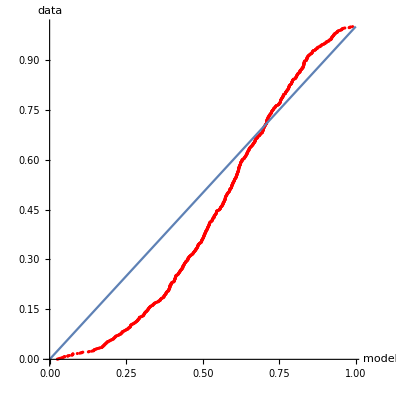

```mathematica
Show[dataplot, lineplot]
```

##### Model 2

```mathematica
Clear[c, a, pdf, distribution, model, compare, dataplot]
```

```mathematica
c= c/.NSolve[Integrate[c*x *E^(-a*x), {x, 0, ∞}] == 1, c][[1]]
```

ConditionalExpression[a^2,Re[a]>0]

```mathematica
(*^ 'c' kan ersättas med a^2*)
```

```mathematica
a = a /. NSolve[{Integrate[x^2 *a^2 *E^(-a*x), {x, 0 , ∞}] == μ && a ≥ 0}, a, Reals][[1]];
```

```mathematica
pdf[x_] := a^2*x *E^(-a*x)
```

```mathematica
distribution = ProbabilityDistribution[pdf[x],{x,0,∞}];
```

```mathematica
model = CDF[distribution, sort];
```

```mathematica
compare = Transpose[{model, data}];
```

```mathematica
dataplot = ListPlot[compare,PlotStyle->Red,AxesLabel->{"model","data"},AspectRatio->Automatic];
```

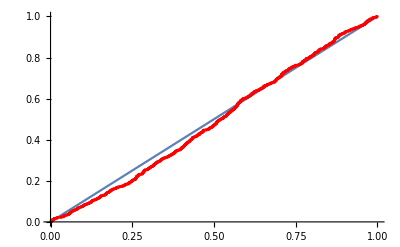

```mathematica
Show[lineplot, dataplot]
```

##### Model 3

```mathematica
Clear[c, a, pdf, distribution, model, compare, dataplot]
```

```mathematica
c= c/.NSolve[Integrate[c * x (x  + b) E^(-a *x), {x, 0, ∞}] == 1, c, Reals][[1]]
```

ConditionalExpression[a^3/(2.+a b),a>0]

```mathematica
(* ^we can replace 'c' with that monstrosity  *)
```

```mathematica
expression[x_] := (a^3/(2 + a * b)) * x * (x + b) * E^(-a*x)
```

```mathematica
{a, b} ={a, b} /. NSolve[{Integrate[x * expression[x], {x, 0 , ∞}] == μ && a ≥ 0,Integrate[x^2 * expression[x], {x, 0 , ∞}] - μ^2 == σ^2 && b≥ 0},{a, b} ][[1]]
```

{0.51767,2.38647}

```mathematica
pdf[x_] := (a^3/(2 + a * b))*x*(x+b)*E^(-a*x) (* Model function *)
```

```mathematica
distribution = ProbabilityDistribution[pdf[x],{x,0,∞}];
```

```mathematica
model = CDF[distribution, sort];
```

```mathematica
compare = Transpose[{model, data}];
```

```mathematica
dataplot = ListPlot[compare,PlotStyle->Red,AxesLabel->{"model","data"},AspectRatio->Automatic];
```

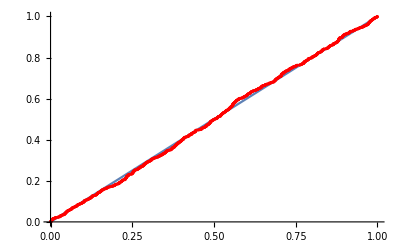

```mathematica
Show[lineplot, dataplot]
```

#### Discussion

Below are diagrams for one of our outcomes with the models.

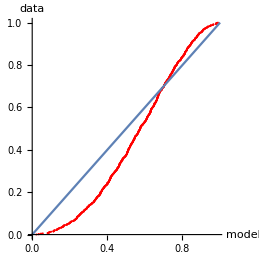
pdf(x)∝e^(-a x),x≥0
-Graphics-

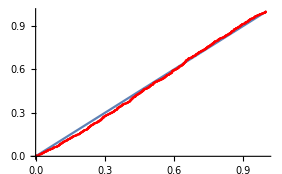
pdf(x)∝x e^(-a x),x≥0
-Graphics-

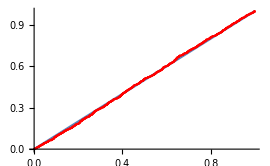
pdf(x)∝x (x+b)e^(-a x),x≥0
-Graphics-

As we can see, the data fit the third model the best so we chose that one.

### Section.Subsection 95% confidence intervals for the constants

#### Solution

#### Code

## Section. Which distribution?

### Section.Subsection Determine a distribution model and point estimates for parameters

#### Solution

To determine the distribution model of the random data we can use the built-in function FindDistribution, which takes a list of values and returns a distribution The function EstimatedDistribution estimates the parameters, and returns a distribution. This only works reliably when we use a large enough sample size (so we used 1000 random numbers).  Then we plotted the distribution with probability plot to verify it.

#### Code

##### Distribution 1

```mathematica
ClearAll["`*"]
```

```mathematica
n = 1000;
```

```mathematica
rand = randomNumber[1, n];
μ= Mean[rand];
FindDistribution[rand]
```

ExponentialDistribution[4.54905]

```mathematica
distribution = EstimatedDistribution[rand, ExponentialDistribution[λ]]
```

ExponentialDistribution[4.54905]

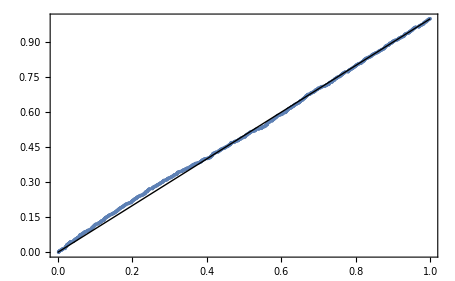

```mathematica
ProbabilityPlot[rand, distribution]
```

##### Distribution 2

```mathematica
ClearAll["`*"]
```

```mathematica
n = 1000;
rand = randomNumber[2, n];
FindDistribution[rand]
```

GeometricDistribution[0.066107]

GeometricDistribution[0.066107]

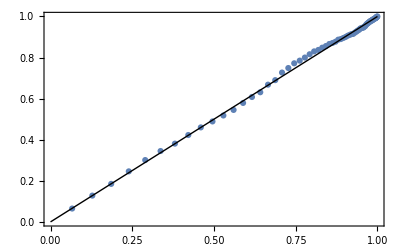

```mathematica
distribution=EstimatedDistribution[rand,GeometricDistribution[p]]
ProbabilityPlot[rand,distribution]
```

##### Distribution 3

```mathematica
ClearAll["`*"]
```

```mathematica
n = 1000;
```

```mathematica
numbers = randomNumber[3, n];
FindDistribution[numbers]
```

GammaDistribution[8.41384,1.54962]

```mathematica
distribution=EstimatedDistribution[numbers,GammaDistribution[α,β]]
```

GammaDistribution[7.88368,1.6038]

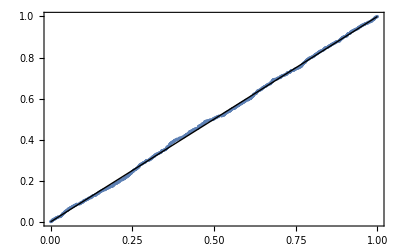

```mathematica
ProbabilityPlot[numbers, distribution]
```

##### Distribution 4

```mathematica
ClearAll["`*"]
```

```mathematica
n = 1000;
```

```mathematica
numbers = randomNumber[4, n];
FindDistribution[numbers]
```

NormalDistribution[2.90454,5.08536]

```mathematica
distribution=EstimatedDistribution[numbers, NormalDistribution[μ,σ]]
```

NormalDistribution[2.90454,5.08536]

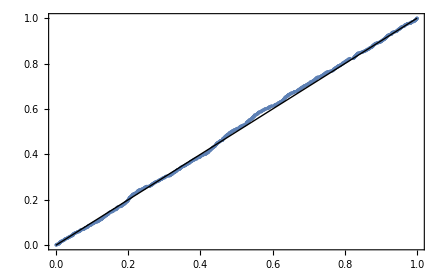

```mathematica
ProbabilityPlot[numbers, distribution]
```

##### Distribution 5

```mathematica
n = 1000;
```

```mathematica
numbers = randomNumber[5, n];
FindDistribution[numbers]
```

BinomialDistribution[10,0.337417]

```mathematica
distribution = EstimatedDistribution[numbers, BinomialDistribution[num, p]]
```

BinomialDistribution[10,0.3289]

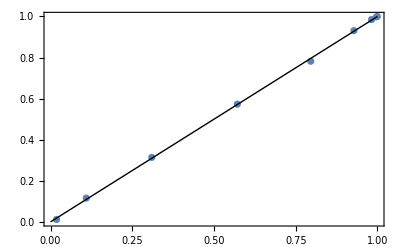

```mathematica
ProbabilityPlot[numbers, distribution]
```

##### Distribution 6

```mathematica
ClearAll["`*"]
```

```mathematica
n = 1000;
```

```mathematica
numbers = randomNumber[6, n];
FindDistribution[numbers]
```

PoissonDistribution[9.743]

```mathematica
distribution = EstimatedDistribution[numbers, PoissonDistribution[μ]]
```

PoissonDistribution[9.743]

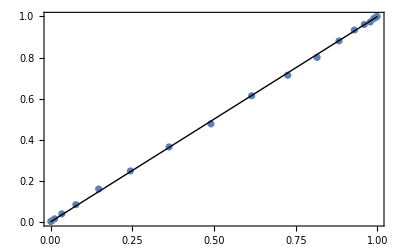

```mathematica
ProbabilityPlot[numbers, distribution]
```

### Section.Subsection Confidence intervals for parameters

#### Solution

To find the confidence interval for the parameters we first create a large matrix of 100 lists, consisting of 1000 elements. Each of those lists are entered into EstimatedDistribution to let Mathematica calculate a list of estimated parameters. Entering those into into MeanCI gives us the interval.

#### Code

##### Distribution 1 (Exponential distribution)

```mathematica
ClearAll["`*"]
```

```mathematica
Needs["HypothesisTesting`"]
```

```mathematica
amountOfLists=100;
```

```mathematica
listLength=1000;
```

```mathematica
matrixOfRands=randomNumber[1,{amountOfLists,listLength}];
```

```mathematica
findλ[data_]:=List@@EstimatedDistribution[data,ExponentialDistribution[λ]];
```

```mathematica
{λlist}=Transpose[findλ/@matrixOfRands];
```

```mathematica
{confλLow, confλHigh}=MeanCI[λlist, ConfidenceLevel->0.95]
```

{4.46222,4.51455}

```mathematica
(1 - confλLow /confλHigh) * 100 (* The percentual difference *)
```

1.15907

##### Distribution 2 (Geometric distribution)

```mathematica
ClearAll["`*"]
```

```mathematica
amountOfLists=100;
```

```mathematica
listLength=1000;
```

```mathematica
matrixOfRands=randomNumber[2,{amountOfLists,listLength}];
```

```mathematica
findp[data_]:=List@@EstimatedDistribution[data,GeometricDistribution[p]]
```

```mathematica
{prob}=Transpose[findp/@matrixOfRands];
```

```mathematica
{confpLow, confpHigh}=MeanCI[prob, ConfidenceLevel->0.95]
```

{0.0647069,0.0654525}

```mathematica
(confpHigh+confpLow)/2 (* The percentual difference *)
```

0.0650797

```mathematica
(1 - confpLow /confpHigh) * 100 (* The percentual difference *)
```

1.13918

##### Distribution 3 (Gamma distribution)

```mathematica
ClearAll["`*"]
```

```mathematica
amountOfLists=100;
```

```mathematica
listLength=1000;
```

```mathematica
matrixOfRands=randomNumber[3,{amountOfLists,listLength}];
```

```mathematica
findαandβ[data_]:=List@@EstimatedDistribution[data,GammaDistribution[α,β]]
```

```mathematica
{αlist,βlist}=Transpose[findαandβ/@matrixOfRands];
```

```mathematica
{confαLow, confαHigh}=MeanCI[αlist, ConfidenceLevel->0.95]
```

{7.98587,8.12054}

```mathematica
(1 - confαLow /confαHigh) * 100 (* The percentual difference *)
```

1.65839

```mathematica
{confβLow, confβHigh}=MeanCI[βlist, ConfidenceLevel->0.95]
```

{1.57702,1.60444}

```mathematica
(1 - confβLow /confβHigh) * 100  (* The percentual difference *)
```

1.70896

##### Distribution 4 (Normal distribution)

```mathematica
ClearAll["`*"]
```

```mathematica
amountOfLists=100;
```

```mathematica
listLength=1000;
```

```mathematica
matrixOfRands=randomNumber[4,{amountOfLists,listLength}];
```

```mathematica
findμandσ[data_]:=List@@EstimatedDistribution[data,NormalDistribution[μ, σ]]
```

```mathematica
{μlist,σlist}=Transpose[findμandσ/@matrixOfRands];
```

```mathematica
confμ = MeanCI[μlist, ConfidenceLevel->0.95]
```

{2.94071,3.00298}

```mathematica
{confσLow, confσHigh} = MeanCI[σlist, ConfidenceLevel->0.95]
```

{4.96569,5.00654}

```mathematica
(1 - confσLow /confσHigh) * 100  (* The percentual difference *)
```

0.815886

##### Distribution 5 (Binomial distribution)

```mathematica
ClearAll["`*"]
```

```mathematica
amountOfLists=100;
```

```mathematica
listLength=1000;
```

```mathematica
matrixOfRands=randomNumber[5,{amountOfLists,listLength}];
```

```mathematica
findmandp[data_]:=List@@EstimatedDistribution[data,BinomialDistribution[listLength ,p]]
```

```mathematica
{m, plist}=Transpose[findmandp/@matrixOfRands];
```

```mathematica
{confpLow, confpHigh}=MeanCI[plist, ConfidenceLevel->0.95]
```

{0.00329518,0.00331466}

```mathematica
(1 - confpLow /confpHigh) * 100 (* The percentual difference *)
```

0.587437

##### Distribution 6 (Poisson distribution)

```mathematica
amountOfLists=100;
```

```mathematica
listLength=1000;
```

```mathematica
matrixOfRands=randomNumber[6,{amountOfLists,listLength}];
```

```mathematica
findμ[data_]:=List@@EstimatedDistribution[data,PoissonDistribution[μ]]
```

```mathematica
{μlist}=Transpose[findμ/@matrixOfRands];
```

```mathematica
{confμLow, confμHigh}=MeanCI[μlist, ConfidenceLevel->0.95]
```

{9.79524,9.83418}

```mathematica
(1 - confμLow /confμHigh)*100 (* The percentual difference *)
```

0.395992